Hi there! These functions might help you think about the bonus problem computationally. Let’s first define two graphs for this example.

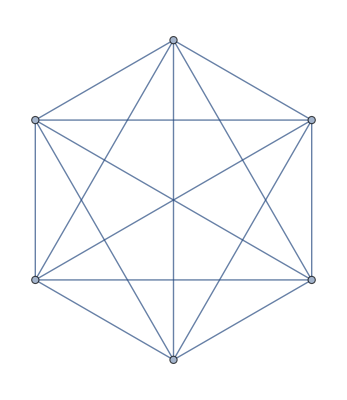

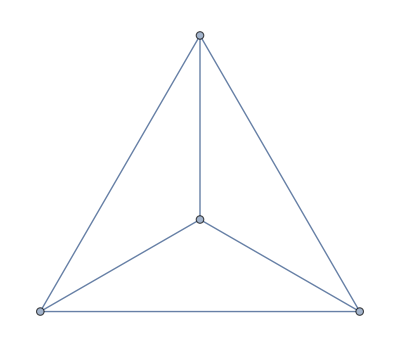

```mathematica
g = CompleteGraph[6]
gprime = WheelGraph[4]
```

The GJoin function below creates the join of two graphs. The other two functions are just helpers I use in the definition. There’s probably a more efficient way to do this.

```mathematica
EdgeShift[edge_, shift_]:=edge[[1]]+shift <-> edge[[2]] + shift
JoinEdges[g1_,g2_]:= Flatten[Outer[#1<->#2&,VertexList[g1],VertexList[g2]+Length[VertexList[g1]]], 1]
GJoin[g1_, g2_] :=EdgeAdd[EdgeAdd[VertexAdd[g1, VertexList[g2]+Length[VertexList[g1]]],EdgeShift[#,Length[VertexList[g1]]]&/@EdgeList[g2]], JoinEdges[g1,g2]]
```

Now, let’s join the g and gprime.

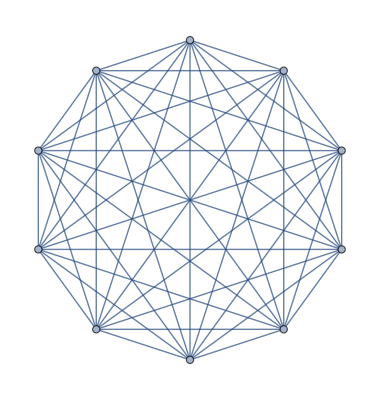

```mathematica
gj = GJoin[g, gprime]
```

That might suspiciously look like the complete graph on 10 vertices to you. It is indeed! We can confirm this by checking for an isomorphism.

```mathematica
IsomorphicGraphQ[gj, CompleteGraph[10]]
```

True

You’ll want to know the chromatic number of a graph. I have a nifty function to evaluate that:

```mathematica
ChromaticNumber[g_]:=MinValue[{k,k>0 && ChromaticPolynomial[g, k]>0 },k,Integers]
```

Let’s check the chromatic number of our graph. From your last homework problem on HW6, you expect it to be 10.

```mathematica
ChromaticNumber[gj]
```

10

Here are some more helpful things you might consider using:

First, we can delete a random number of edges from a graph and then compute its chromatic number. These graphs are candidates for a graph that has chromatic number 10 and are potentially biplanar. You’d have to prove that they’re biplanar, i.e. they have thickness 2.

```mathematica
graph = CompleteGraph[11];
numEdges = 2;
numSamples= 10;
Map[ChromaticNumber[#]&,Map[EdgeDelete[#, RandomSample[EdgeList[#],numEdges]]&,Table[graph, {numSamples}]]]
```

{10,9,9,9,10,10,10,10,9,9}

Another way to think about this is to consider making  a random subgraph of a graph. Then, evaluate the graph difference to see if both subgraphs are planar. If they are and your union is a graph with your desired chromatic number, you just found an example!

```mathematica
RandomSubgraph[g_?GraphQ,s_]:=Subgraph[g,RandomSample[VertexList[g],s]]
```

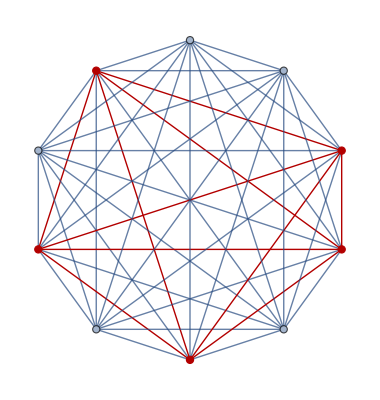
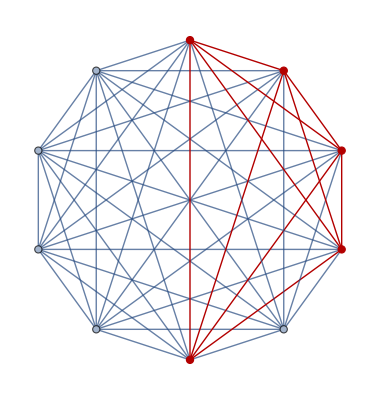
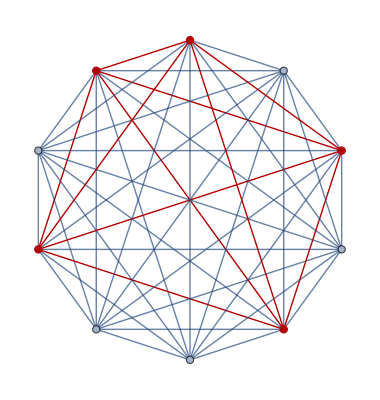
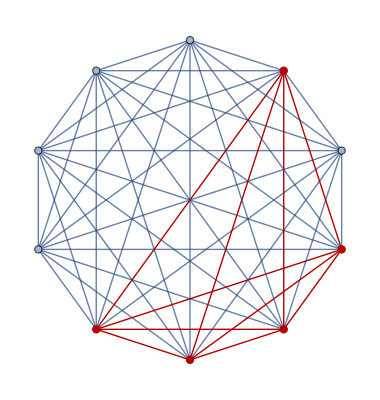
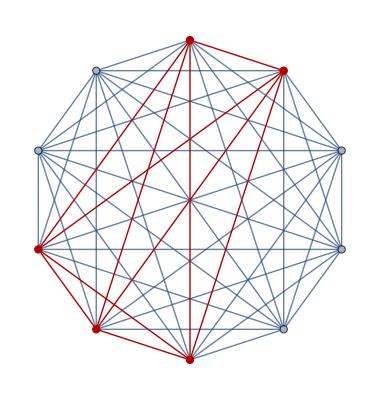
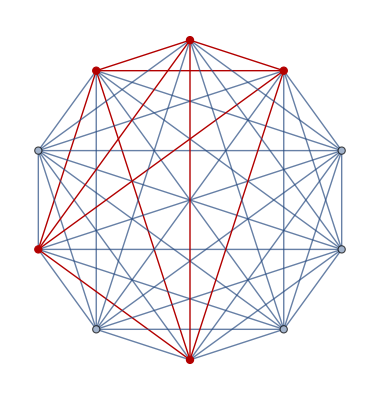
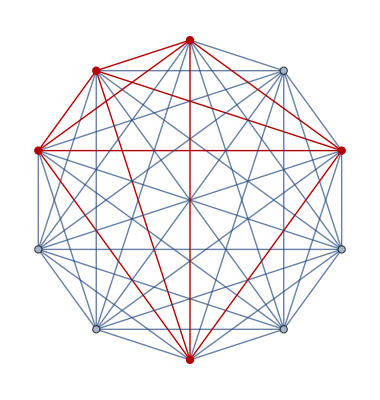
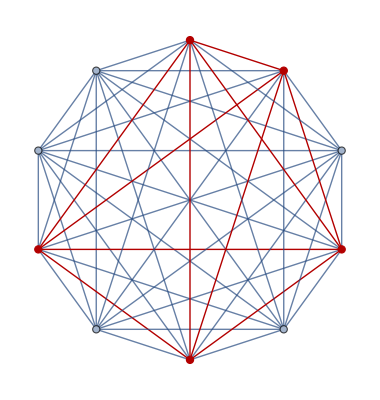
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[HighlightGraph[gj,RandomSubgraph[gj,5]],{10}]
```